# Boundary Layer Theory

## Assuming one boundary layer

```mathematica
Clear[x,y,ϵ,δ]
```

### Identify Boundary Layer

Compute the ODE for boundary conditions at  and

```mathematica
a = 0;
b = Pi/2; 

ODE = ϵ*y''[x] - (1/(4 + Sin[x])) y'[x] +  y[x]
BCa = y[a] - 1
BCb = y[b] - 1
```

y[x]-y'[x]/(4+Sin[x])+ϵ y''[x]

-1+y[0]

-1+y[π/2]

We can plot the ODE to find where the boundary layer is

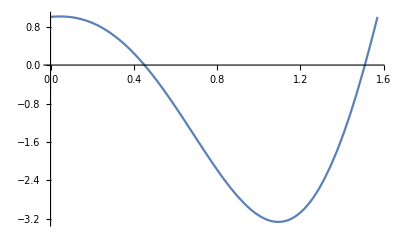

```mathematica
ϵ = 0.1;

sol = NDSolve[{ODE == 0, BCa == 0, BCb == 0}, y[x], x];
num[x_] := Evaluate[y[x]/. sol[[1]]]; 
Plot[num[x], {x,a,b}]

Clear[ϵ]
```

Now that we have found where the boundary layer is, let’s do real math...
Hopefully our ODE is of the from:  where  determines the location of the boundary layer as following
If  on  then the boundary layer is on  (left)
If  on  then the boundary layer is on  (right)
If  has a sign switch on , then the boundary layer is internal and we expect it to be at  such that  (internal)
If  or  on , then there might two boundary layers, at  and   respectively.

### Dominant Balance

Now that we have found were the boundary layer is, we compute the dominant balance:

#### Boundary layer at (left)

Define the stretched variable as   and then our ODE becomes (chain rule)

```mathematica
ODEii = ODE /. {y''[x] -> 1/(δ^2)y''[ξ],y'[x] -> 1/(δ)y'[ξ],y[x] -> y[ξ], x -> δ*ξ+a}
```

Compute the dommy balance by finding the lowest power of  that is not attached to  and setting it equal to the one that does have a ϵ term.

```mathematica
δ = ϵ;
```

Plugging in our inner variables and dividing  by  yields

```mathematica
ODEi = ODEii / (ϵ/δ^2)
```

#### Boundary layer at

Define the stretched variable as  and then our ODE becomes (chain rule)

```mathematica
Clear[δ]
ODEii = ODE /. {y''[x] -> 1/(δ^2)y''[ξ],y'[x] -> -1/(δ)y'[ξ],y[x] -> y[ξ], x -> b-(δ*ξ)}
```

y[ξ]+y'[ξ]/(δ (4+Sin[δ ξ]))+(ϵ y''[ξ])/δ^2

Compute the dommy balance by finding the lowest power of  that is not attached to  and setting it equal to the one that does have a  term.

```mathematica
δ = ϵ;
```

Plugging in our inner variables and dividing by  yields

```mathematica
ODEi = ODEii / (ϵ/δ^2)
```

ϵ (y[ξ]+y'[ξ]/(ϵ (4+Sin[ϵ ξ]))+y''[ξ]/ϵ)

### Outer Layer

Plug in the correct boundary layer corresponding to the outer layer

```mathematica
(*BCo = BCb *)(*USE WHEN BL IS ON LEFT *)
BCo = BCa (*USE WHEN BL IS ON RIGHT*)
```

-1+y[0]

Assume the expansion of the outer problem is of the form

```mathematica
Clear[ϵ,y,y1,y2]
y[x_] = y0[x] + ϵ*y1[x] + ϵ^2*y2[x];
```

Plugging in the expansion gives

```mathematica
ODE
BCo
```

y0[x]+ϵ y1[x]+ϵ^2 y2[x]-(y0'[x]+ϵ y1'[x]+ϵ^2 y2'[x])/(4+Sin[x])+ϵ (y0''[x]+ϵ y1''[x]+ϵ^2 y2''[x])

-1+y0[0]+ϵ y1[0]+ϵ^2 y2[0]

Collecting terms yields

```mathematica
ODEos = Simplify[Coefficient[ODE,ϵ,{0,1,2}]];
BCos = Coefficient[BCo,ϵ,{0,1,2}];

MatrixForm[Transpose[ODEos]]
MatrixForm[Transpose[BCos]]
```

(y0[x]-y0'[x]/(4+Sin[x])
y1[x]-y1'[x]/(4+Sin[x])+y0''[x]
y2[x]-y2'[x]/(4+Sin[x])+y1''[x])

(-1+y0[0]
y1[0]
y2[0])

#### Leading Orders

Compute the leading order solution

```mathematica
sol = DSolve[{ODEos[[1]] == 0, BCos[[1]]==0},y0[x],x];
yo0[x_] = y0[x] /. sol[[1]]
```

ⅇ^(1+4 x-Cos[x])

#### Higher Orders

In the case of solving higher orders

```mathematica
sol = DSolve[{(ODEos[[2]]/.{y0 -> yo0}) == 0, BCos[[2]]==0},y1[x],x];
yo1[x_] = y1[x] /. sol[[1]]
```

### Inner Layer

Plug in the correct boundary layer corresponding to the inner layer

```mathematica
Clear[ϵ,y,y1,y2]
(*BCi = BCa*) (*USE WHEN BL IS ON LEFT*)
BCi = BCb (*USE WHEN BL IS ON RIGHT*)
```

-1+y[π/2]

Assume the expansion of the inner problem is of the form

```mathematica
y[ξ_] = y0[ξ] + ϵ*y1[ξ] + ϵ^2*y2[ξ];
```

Plugging in the expansion gives

```mathematica
ODEi
BCi
```

ϵ (y0[ξ]+ϵ y1[ξ]+ϵ^2 y2[ξ]+(y0'[ξ]+ϵ y1'[ξ]+ϵ^2 y2'[ξ])/(ϵ (4+Sin[ϵ ξ]))+(y0''[ξ]+ϵ y1''[ξ]+ϵ^2 y2''[ξ])/ϵ)

-1+y0[π/2]+ϵ y1[π/2]+ϵ^2 y2[π/2]

Collecting terms yields

```mathematica
ODEis = Simplify[Coefficient[ODEi,ϵ,{0,1,2}]];
BCis = Coefficient[BCi,ϵ,{0,1,2}];

MatrixForm[Transpose[ODEis]]
MatrixForm[Transpose[BCis]]
```

(y0'[ξ]/(4+Sin[ϵ ξ])+y0''[ξ]
y0[ξ]+y1'[ξ]/(4+Sin[ϵ ξ])+y1''[ξ]
y1[ξ]+y2'[ξ]/(4+Sin[ϵ ξ])+y2''[ξ])

(-1+y0[π/2]
y1[π/2]
y2[π/2])

#### Leading Orders

Compute the leading order solution

```mathematica
sol = DSolve[{ODEis[[1]] == 0, BCis[[1]]==0},y0[ξ],ξ] /. {C[1] -> c};
yi0[ξ_] = Simplify[y0[ξ] /. sol[[1]]]
```

1/(15 ⅈ+(1+4 ⅈ) √15)(15 ⅈ+(1+4 ⅈ) √15+15 ((1+4 ⅈ)+ⅈ √15) c Hypergeometric2F1[1,-ⅈ/(√15 ϵ),1-ⅈ/(√15 ϵ),((-15 ⅈ+(1+4 ⅈ) √15) (15 ⅈ+√15+4 √15 Tan[(π ϵ)/4]))/((15 ⅈ+(1+4 ⅈ) √15) (-15 ⅈ+√15+4 √15 Tan[(π ϵ)/4]))] (1-ⅈ/(√15)-(4 ⅈ Tan[(π ϵ)/4])/(√15))^(-ⅈ/(√15 ϵ)) (1+ⅈ/(√15)+(4 ⅈ Tan[(π ϵ)/4])/(√15))^(ⅈ/(√15 ϵ))-15 ⅈ ((4-ⅈ)+√15) c Hypergeometric2F1[1,-ⅈ/(√15 ϵ),1-ⅈ/(√15 ϵ),((15+(4+ⅈ) √15) (15 ⅈ+√15+4 √15 Tan[(π ϵ)/4]))/((-15+(4+ⅈ) √15) (-15 ⅈ+√15+4 √15 Tan[(π ϵ)/4]))] (1-ⅈ/(√15)-(4 ⅈ Tan[(π ϵ)/4])/(√15))^(-ⅈ/(√15 ϵ)) (1+ⅈ/(√15)+(4 ⅈ Tan[(π ϵ)/4])/(√15))^(ⅈ/(√15 ϵ))-15 ⅈ ((4-ⅈ)+√15) c Hypergeometric2F1[1,-ⅈ/(√15 ϵ),1-ⅈ/(√15 ϵ),((-15 ⅈ+(1+4 ⅈ) √15) (15 ⅈ+√15+4 √15 Tan[(ϵ ξ)/2]))/((15 ⅈ+(1+4 ⅈ) √15) (-15 ⅈ+√15+4 √15 Tan[(ϵ ξ)/2]))] (1-ⅈ/(√15)-(4 ⅈ Tan[(ϵ ξ)/2])/(√15))^(-ⅈ/(√15 ϵ)) (1+ⅈ/(√15)+(4 ⅈ Tan[(ϵ ξ)/2])/(√15))^(ⅈ/(√15 ϵ))+15 ((1+4 ⅈ)+ⅈ √15) c Hypergeometric2F1[1,-ⅈ/(√15 ϵ),1-ⅈ/(√15 ϵ),((15+(4+ⅈ) √15) (15 ⅈ+√15+4 √15 Tan[(ϵ ξ)/2]))/((-15+(4+ⅈ) √15) (-15 ⅈ+√15+4 √15 Tan[(ϵ ξ)/2]))] (1-ⅈ/(√15)-(4 ⅈ Tan[(ϵ ξ)/2])/(√15))^(-ⅈ/(√15 ϵ)) (1+ⅈ/(√15)+(4 ⅈ Tan[(ϵ ξ)/2])/(√15))^(ⅈ/(√15 ϵ)))

#### Higher Orders

In the case of solving higher orders

```mathematica
sol = DSolve[{(ODEis[[2]]/.{y0 -> yi0}) == 0, BCis[[2]]==0},y1[ξ],ξ] /. {C[1] -> d};
yi1[ξ_] = y1[ξ] /. sol[[1]]
```

### Matching

Match the limits and solve for the undetermined constants

```mathematica
Clear[ϵ,c]
match1 = Limit[yi0[ξ],ξ -> ∞]
(*match2 = Limit[yo0[x], x -> a]*) (*USE WHEN BOUNDARY IS ON LEFT*)
match2 = Limit[yo0[x], x -> b] (*USE WHEN BOUNDARY IS ON RIGHT*)
sol = Solve[match1 == match2, c]
yi0[ξ_] = yi0[ξ] /. sol[[1]]

(*yU[x_,ϵ_] = yo0[x] + yi0[(x-a)/δ] - match2*) (*USE WHEN BOUNDARY IS ON LEFT*)
yU[x_,ϵ_] = yo0[x] + yi0[(b-x)/δ] - match2 (*USE WHEN BOUDNARY IS ON RIGHT*)
```

### Overkill Plots

```mathematica
Clear[y]
ϵ = 0.01

sol = NDSolve[{ODE == 0, BCa == 0, BCb == 0}, y[x], x];
num[x_] := Evaluate[y[x]/. sol[[1]]]; 
Plot[{num[x],yU[x,ϵ]}, {x,a,b}, PlotLegends -> {"Exact","Approx"}]

Clear[ϵ]
```